## Задание 3

## Метод коллокации

```mathematica
ϕ[x_,i_] := x^(2 i - 2) (1 - x^2);
mass = {0, -1/2, 1/2};
```

```mathematica
a[i_, j_]:= Derivative[2,0][ϕ][mass⟦i+1⟧, j] + (1 + mass⟦i+1⟧^2) ϕ[mass⟦i+1⟧, j];
b[i_] := -1;
```

```mathematica
A = Table[a[i,j],{i, 1,2}, {j, 1, 2}];
B = Table[b[i],{i, 1, 2}];
abs = LinearSolve[A,B]
```

{16/17,0}

```mathematica
y2[x_]:= Sum[abs⟦i⟧ϕ[x,i],{i,1,2}]
```

```mathematica
p1 = Plot[y2[x],{x,-1,1},PlotLegends->LineLegend[{ColorData["HTML","Black"]}, {"Метод коллокации"}],PlotStyle->ColorData["HTML","Black"] ,PlotTheme-> "Detailed"];
```

## Точное решение

```mathematica
sol = NDSolve[{y''[x] + (1 + x^2) y[x] == -1, y[-1] == 0, y[1] == 0},y,{x,-1,1}]⟦1⟧
```

{y→InterpolatingFunction[…]}

```mathematica
p2 = Plot[y[x]/.sol, {x, -1, 1},PlotLegends->LineLegend[{ColorData["HTML","MidnightBlue"]}, {"Точное решение"}],PlotStyle->ColorData["HTML","MidnightBlue"] ,PlotTheme-> "Detailed"];
```

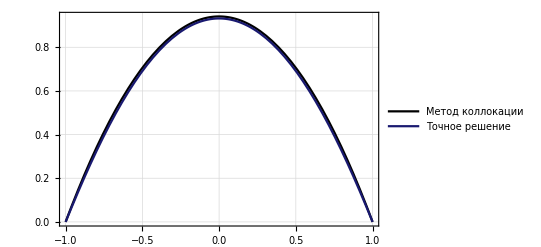

```mathematica
Show[p1, p2]
```

## Интегральный метод наименьших квадратов

```mathematica
Lϕ[x_, i_] := Derivative[2,0][ϕ][x, i] + (1 + x^2) ϕ[x, i];
a1[i_, j_] := Integrate[Lϕ[x,i] Lϕ[x, j],{x,-1,1}];
b1[i_] := Integrate[ -Lϕ[x, i], {x, -1, 1}];
```

```mathematica
A1 = Table[a1[i,j],{i,1,2}, {j, 1, 2}];
```

```mathematica
B1 = Table[b1[i], {i,1,2}];
```

```mathematica
abc1 = LinearSolve[A1,B1]
```

{31755933/34046644,-2321319/34046644}

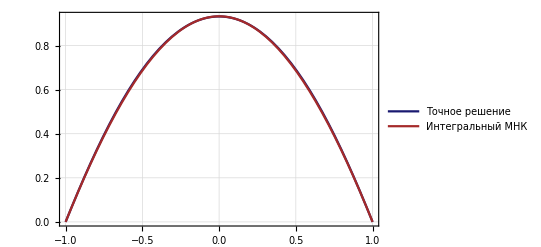

```mathematica
y21[x_] = Sum[abc1⟦i⟧ϕ[x,i],{i,1,2}];
p3 = Plot[y21[x],{x,-1,1},PlotLegends->LineLegend[{ColorData["HTML","Brown"]}, {"Интегральный МНК"}],PlotStyle->ColorData["HTML","Brown"] ,PlotTheme-> "Detailed"];
Show[p2,p3]
```

## Дискретный метод наименьших квадратов

```mathematica
Lϕ1[i_, j_] := Derivative[2,0][ϕ][mass⟦i+1⟧, j] + (1 + mass⟦i+1⟧^2) ϕ[mass⟦i+1⟧, j];
a2[i_, j_] := Sum[Lϕ1[k,i] Lϕ1[k, j],{k,1,2}];
b2[i_] := -Sum[ Lϕ1[k, i], {k, 1, 2}];
```

```mathematica
A2 = Table[a2[i,j],{i, 1, 2}, {j,1,2}];
```

```mathematica
B2 = Table[b2[i], {i,1,2}];
```

```mathematica
abc2 = LinearSolve[A2,B2]
```

{16/17,0}

```mathematica
y22[x_] = Sum[abc2⟦i⟧ϕ[x,i],{i,1,2}];
p4 = Plot[y22[x],{x,-1,1},PlotLegends->LineLegend[{ColorData["HTML","Red"]}, {"Дискретный МНК"}],PlotStyle->ColorData["HTML","Red"] ,PlotTheme-> "Detailed"];
```

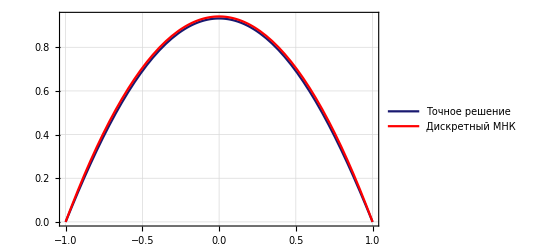

```mathematica
Show[p2,p4, PlotRange->All]
```

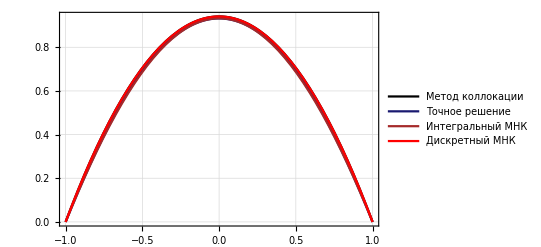

```mathematica
plS3 = Show[p1,p2,p3,p4, PlotRange->All]
```

```mathematica
Export["plS3.pdf",plS3]
Export["plS3.jpg",plS3]
```

plS3.pdf

plS3.jpg

## Задание 4 Галеркин

## ∑_(j=1)^n a_ij c_j =d_i

```mathematica
ϕ[x_,i_]:=x^i (1-x);
a = 0 ; b = 1;
a3[i_,j_] :=Internal`InheritedBlock[{Power},Unprotect[Power];
Power[0,0]=1; ϕ[b,i]Derivative[1,0][ϕ][b, j]  - ϕ[a,i] Derivative[1,0][ϕ][a, j] - Integrate[Derivative[1,0][ϕ][x, j] Derivative[1,0][ϕ][x, i],{x,a,b}] + Integrate[ϕ[x,j] ϕ[x,i],{x,a,b}]];
```

```mathematica
d3[i_]:= Integrate[-x ϕ[x,i],{x,a,b}];
```

```mathematica
A3[n_] := Table[a3[i,j],{i,1,n},{j,1,n}];
D3[n_] := Table[d3[i], {i,1,n}];
```

```mathematica
abc3[n_] := LinearSolve[A3[n],D3[n]];
```

```mathematica
fu1= abc3[2]
fu2 = abc3[3]
```

{71/369,7/41}

{13811/73554,2380/12259,-7/299}

```mathematica
solG2[x_]:=Sum[fu1⟦i⟧ ϕ[x,i], {i,1,2}];
```

```mathematica
solG3[x_]:=Sum[fu2⟦i⟧ ϕ[x,i], {i,1,2}];
```

```mathematica
pg1 = Plot[solG2[x], {x,0,1},PlotLegends->LineLegend[{ColorData["HTML","Brown"]}, {"Метод Галеркина для n = 2"}],PlotStyle->ColorData["HTML","Brown"] ,PlotTheme-> "Detailed"];
```

```mathematica
pg2 = Plot[solG3[x], {x, 0, 1},PlotLegends->LineLegend[{ColorData["HTML","MidnightBlue"]}, {"Метод Галеркина для n = 3"}],PlotStyle->ColorData["HTML","MidnightBlue"] ,PlotTheme-> "Detailed"];
```

## Точное решение

```mathematica
sol2 = DSolve[{y''[x] + y[x] == -x, y[0] == 0, y[1] == 0},y,x]⟦1⟧
```

{y→Function[{x},-x+Csc[1] Sin[x]]}

```mathematica
pgE = Plot[y[x]/.sol2,{x,0,1},PlotLegends->LineLegend[{Black}, {"Точное решение"}],PlotStyle->Black ,PlotTheme-> "Detailed"];
```

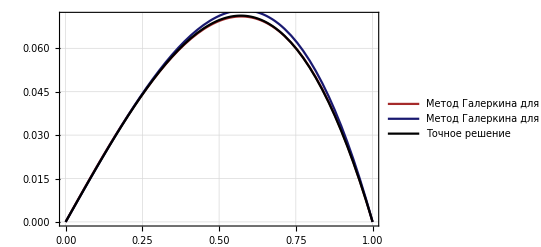

```mathematica
plS4 = Show[pg1, pg2, pgE]
```

```mathematica
Export["plS4.pdf",plS4]
Export["plS4.jpg",plS4]
```

plS4.pdf

plS4.jpg